```mathematica
91PC
```

```mathematica
s=NDSolve[{y''[x]+Sin[y[x]] y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {y[x]+Sin[y[x]] y[x]==0,y[0]==1,True}.

NDSolve[{y[x]+Sin[y[x]] y[x]==0,y[0]==1,True},y,{x,0,30}]

```mathematica
s=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
s=NDSolve[{y''[x]+Sin[y[x]] y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {y[x]+Sin[y[x]] y[x]==0,y[0]==1,True}.

NDSolve[{y[x]+Sin[y[x]] y[x]==0,y[0]==1,True},y,{x,0,30}]

```mathematica
Clear[Derivative]
```

```mathematica
s=NDSolve[{y''[x]-y[x]+(y[x])^2==0,y[0]==0.9,y'[0]==0},y,{x,0,5}]
```

{{y→InterpolatingFunction[{{0., 5.}}, <>]}}

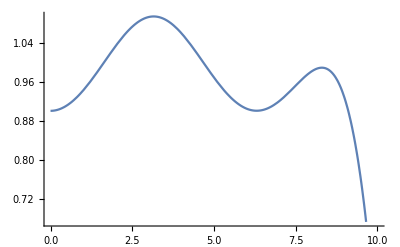

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,10},PlotStyle->Automatic]
```

```mathematica
Integrate x/(x-1)
```

(Integrate x)/(-1+x)

```mathematica
Integrate[1/Sqrt[x^2+2x^3/3],x]
```

-(2 x √(3+2 x) ArcTanh[√(1+(2 x)/3)])/(√(x^2 (3+2 x)))

```mathematica
FullSimplify[Integrate[1/Sqrt[x^2+2x^3/3],x]]
```

-(2 x √(3+2 x) ArcTanh[√(1+(2 x)/3)])/(√(x^2 (3+2 x)))